## Trebuchet Simulation

```mathematica
(* This function sets up and solves the Legrangian for the trebuchet.*)
simulateTrebuchetHelper[ma_,mh_,m_,M_,mw_,mf_,L_,l_,h_,Rw_,α_,θ0_,ϕ0_,t0_,tf_,plot_]:=Module[
{g,Ia,Ih,Iw,xm,ym,xa,ya,xh,yh,xM,yM,Tm,Ta,Th,TM,Tw,Tframe,T,U,LL,NCtorque,θeqn,ϕeqn,xeqn,dap,L0,θdot0,ϕdot0,x0,xdot0,soln,θ,ϕ,x,v,vm},
g=9.81;

(* The following are constant across all simulations. *)

(* Masses; all in [kg]. *)
ma=81.7*10^-3; (* Mass of the arm until the pivot point, measured from the left. *)
mh=10^-6; (* Mass of the arm from the pivot point until the arm's end, on the right. We set mh = 0 here and lump what mh actually is into the counterweight mass because the connector is definitely not a rod so we can't really get its angular momentum via simple approximations. *)
m=16.4*10^-3; (* Mass of the projectile. *)

(* Various lengths; all in [m]. *)
L=40.7*10^-2;
l=21.0*10^-2;
h=8.7*10^-2;

(* Radius of each wheel in [m]. *)
Rw=1.55*10^-2;
t0=0;
tf=5;

(* ϕ0 [rad]. *)
ϕ0=0;

(* Rotational inertias, all in the standard SI units of [kg m^2]. *)
Ia=1/12 ma(L+l)^2;
Ih=1/12 mh h^2;
Iw=1/2 mw Rw^2; (* We approximate each wheel as a cylinder of uniform mass mw and radius Rw. *)
(* ====================================================================================== *)
(* Transformation equations. *)
xm[t_]:=x[t]-L Cos[θ[t]];
ym[t_]:=L Sin[θ[t]];

xa[t_]:=x[t]-(L-l)/2 Cos[θ[t]];
ya[t_]:=(L-l)/2 Sin[θ[t]];

xh[t_]:=x[t]+l Cos[θ[t]]+h/2 Sin[ϕ[t]];
yh[t_]:=l Sin[θ[t]]-h/2 Cos[ϕ[t]];

xM[t_]:=x[t]+l Cos[θ[t]]+h Sin[ϕ[t]];
yM[t_]:=-l Sin[θ[t]]-h Cos[ϕ[t]];
(* ====================================================================================== *)
(* Kinetic energy. *)
Tm=1/2 m(xm'[t]^2+ym'[t]^2);
Ta=1/2 Ia θ'[t]^2+1/2 ma(xa'[t]^2+ya'[t]^2);
Th=1/2 Ih ϕ'[t]^2+1/2 mh(xh'[t]^2+yh'[t]^2);
TM=1/2 M(xM'[t]^2+yM'[t]^2);
Tw=8*(1/2 Iw(x'[t]/Rw)^2+1/2 mw x'[t]^2);
Tframe=1/2 mf x'[t]^2;
T=Tm+Ta+Th+TM+Tw+Tframe;
(* ====================================================================================== *)
(* Potential energy. *)
U=m g ym[t]+ma g ya[t]+mh g yh[t]+M g yM[t];
(* ====================================================================================== *)
(* Legrangian. *)
LL=T-U;
(* ====================================================================================== *)
(* Equations of motion. *)
NCtorque=α L^2 θ'[t]^2(m+1/4 ma);
θeqn=D[D[LL,θ'[t]],t]==D[LL,θ[t]]+NCtorque;
ϕeqn=D[D[LL,ϕ'[t]],t]==D[LL,ϕ[t]];
xeqn = D[D[LL, x'[t]], t] == D[LL, x[t]];

θdot0=0;
ϕdot0=0;
x0=0;
xdot0=0;

soln=NDSolve[
{θeqn,ϕeqn,xeqn,θ[t0]==θ0,ϕ[t0]==ϕ0,x[t0]==x0,θ'[t0]==θdot0,ϕ'[t0]==ϕdot0,x'[t0]== xdot0},
{θ,ϕ,x},
{t,t0,tf}];
θ=θ/.soln[[1,1]];
ϕ=ϕ/.soln[[1,2]];
x=x/.soln[[1,3]];
v[t_]:=x'[t];
vm[t_]=√(xm'[t]^2+ym'[t]^2);
If[plot==1,
{Print[Plot[T+U,{t,t0,tf},PlotRange->{-10,10},PlotLabel->"Total energy vs. time",AxesLabel->Automatic]];
Print[Plot[{θ[t],ϕ[t]},{t,0,tf},PlotRange->{-5,5},PlotLabel->"θ[t] and ϕ[t]",AxesLabel->Automatic,PlotLegends->"Expressions"]];
Print[Plot[x[t],{t,t0,tf},PlotRange->{-5,5},PlotLabel->"x[t]",AxesLabel->Automatic]];
Print[Plot[v[t],{t,t0,tf},PlotRange->{-5,5},PlotLabel->"ẋ[t]",AxesLabel->Automatic]];
Print[Plot[vm[t],{t,t0,tf},PlotRange->{-10,10},PlotLabel->"Velocity of end of throwing arm vs. time",AxesLabel->Automatic]];},{}
];
{θ,ϕ,x,v,vm}
];
```

```mathematica
(* This function is used to simulate various the various trebuchet configurations that we also experimentally observed. To model different configurations, vary the parameter "expParams", which is a list of the form {M, mw, mf, θ0exp, θfexp}. *)
```

```mathematica
simulateTrebuchet[α_,expParams_,plot_]:=Module[
{ma,mh,m,M,mw,mf,L,l,h,Rw,t0,tf,θ0exp,θfexp,ϕ0,θ,ϕ,x,v,vm,vmf,t,tfexp},
(* Unpack configuration-specific parameters. *)
{M,mw,mf,θ0exp,θfexp}=expParams;

(* We are really interested in vm[t], the velocity of the projectile. *)
{θ,ϕ,x,v,vm}=simulateTrebuchetHelper[ma,mh,m,M,mw,mf,L,l,h,Rw,α,θ0exp,ϕ0,t0,tf,0];

(* Now compute the release velocity of the projectile, vmf, by looking at the projectile's velocity at the experimentally determined time of release. *)

tfexp=t/.FindRoot[θ[t]-θfexp,{t,.1}]; (* Here, we assume that the first occurance of θ[t] = θfexp is when t > .1. Why is this okay to assume across all values of α? Well, the intersection point is to the right of t = .1 when α = 0. After looking at some plots of θ[t] for various α, it's apparent that the amplitude of θ[t] decreases as α increases. So, since α ≥ 0, then the intersection point should always occur at t > .1. We tested this by calling this function ("simulateTrebuchet") with an argument of 1 (for "true") passed in for the "plot" parameter. *)

vmf=vm[tfexp];

(* This was used for debugging purposes. *)
If[plot==1,
{
Print["Look at this plot! Make sure to verify that the first intersection of θ[t] with θfexp occurs after t = .1. If this is not the case, then the calculated value of vmf is incorrect."];
Print[Plot[{θ[t],θfexp},{t,0,5},PlotLabel->"θ[t] vs. t",AxesLabel->Automatic,PlotLegends->"Expressions"]];
},
{}];

(* Return stuff (most importantly, vmf). *)
{θ,ϕ,x,v,vm,tfexp,vmf}
]
```

```mathematica
(* Returns two outputs.
1. The α for which the difference between the difference between the theoretically predicted projectile release velocity and the experimentally observed projectile release velocity (vmfexp) is minimized.
2. A table of α values and associated (absolute) differences between theoretical and experimental velocities. The first column contains the α values and the second contains the associated errors. *)
findBestα[αmin_,αmax_,Δα_,expParams_,vmfexp_]:=Module[{bestErr,bestα,α,vmf,err,αlist,errlist,errTable},
bestErr=∞;
bestα=αmax;

αlist={};
errlist={};

(* α should be ≥ 0. *)
For[α=αmin,α≤αmax,α+=Δα,
{
vmf=simulateTrebuchet[α,expParams,0][[7]];
err=Abs[vmfexp-vmf];
If[err<bestErr,
{
bestErr=err;
bestα=α;
},{}];
αlist=Append[αlist,α];
errlist=Append[errlist,err];
}];
errTable=Transpose[{αlist,errlist}];
{bestα,errTable}]
```

```mathematica
(* Now we find the best value of α for each trial. Each trial comes with its own experimentally determined parameters: 
M (counterweight mass), mw (mass of a wheel), mf (mass of the frame), θ0exp (experimentally determined initial θ), θfexp (experimentally determined θ at release of projectile). We will also display a table of α vs. associated error for each trial, so that we can convince ourselves that, for each trial, the α coorresponding to minimal error is attained in a continuous fashion. *)

(* To restate, the following lists of experimental parameters contain the entries: M, mw, mf, θ0exp, θfexp. *)

(* Trial 1 is the control trial. *)
T1expParams={264.4*10^-3,62.5/8*10^-3,151.1*10^-3,-0.533416733,1.399476452}; 
(* In trial 2, the counterweight mass was lowered. *)
T2expParams={238.6*10^-3,62.5/8*10^-3,151.1*10^-3,-0.468261186,1.140126872};
(* In trial 3, the initial θ was decreased. *)
T3expParams={264.4*10^-3,62.5/8*10^-3,151.1*10^-3,-0.025081341,1.56763924};
(* In trial 4, we removed the wheels from the trebuchet before collecting data. We treat 10^6 as basically being ∞, and model the wheel-less trebuchet as having  "infinitely heavy" wheels. *)
inf=10^6; 
T4expParams={264.4*10^-3,inf,inf,-1.102135756,1.318215642};

(* This list contains the experimentally determined velocities for each trial. *)
expVmfs={3.486774447,3.341277277,2.599623061,3.31};

(* Finally, loop over the trials and find the best α for each one. *)
expParams={T1expParams,T2expParams,T3expParams,T4expParams};
bestαList={};
For[i=1,i≤4,i+=1,
{
{α,errTable}=findBestα[0, 5,.25,expParams[[i]],expVmfs[[i]]];
Print[StringForm["Best α for T`` = ", i],α];
bestαList=Append[bestαList,α];
Print[TableForm[errTable,TableHeadings->{{},{"α","error"}}]];
}];
```

NDSolve::ndsz: At t == 2.06133, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-2.20066} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 0.981587, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.749886, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.862128} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.855228} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Best α for T1 = 0.25

| α | error
 | 0 | 0.830481
 | 0.25 | 0.330056
 | 0.5 | 1.41565
 | 0.75 | 2.62326
 | 1. | 4.03512
 | 1.25 | 5.72158
 | 1.5 | 7.75813
 | 1.75 | 10.2322
 | 2. | 13.2477
 | 2.25 | 16.9305
 | 2.5 | 21.4328
 | 2.75 | 26.9404
 | 3. | 33.6799
 | 3.25 | 41.928
 | 3.5 | 52.0232
 | 3.75 | 64.3787
 | 4. | 79.4999
 | 4.25 | 98.0017
 | 4.5 | 120.624
 | 4.75 | 148.225
 | 5. | 181.637

Best α for T2 = 0

| α | error
 | 0 | 0.350619
 | 0.25 | 0.355637
 | 0.5 | 1.14867
 | 0.75 | 2.06467
 | 1. | 3.13905
 | 1.25 | 4.41045
 | 1.5 | 5.92303
 | 1.75 | 7.7285
 | 2. | 9.88797
 | 2.25 | 12.4741
 | 2.5 | 15.5732
 | 2.75 | 19.2882
 | 3. | 23.7411
 | 3.25 | 29.076
 | 3.5 | 35.4624
 | 3.75 | 43.0976
 | 4. | 52.2085
 | 4.25 | 63.0508
 | 4.5 | 75.904
 | 4.75 | 91.0575
 | 5. | 108.782

Best α for T3 = 0.25

| α | error
 | 0 | 0.514377
 | 0.25 | 0.326919
 | 0.5 | 0.517356
 | 0.75 | 1.2244
 | 1. | 2.40665
 | 1.25 | 3.64568
 | 1.5 | 5.05518
 | 1.75 | 6.70769
 | 2. | 8.67356
 | 2.25 | 11.0315
 | 2.5 | 13.8739
 | 2.75 | 17.3118
 | 3. | 21.479
 | 3.25 | 26.5381
 | 3.5 | 32.6871
 | 3.75 | 40.1669
 | 4. | 49.2717
 | 4.25 | 60.3603
 | 4.5 | 73.8714
 | 4.75 | 90.3406
 | 5. | 110.423

Best α for T4 = 0.25

| α | error
 | 0 | 0.672892
 | 0.25 | 0.272926
 | 0.5 | 1.13745
 | 0.75 | 2.0745
 | 1. | 3.20474
 | 1.25 | 4.72766
 | 1.5 | 7.18127
 | 1.75 | 12.8525
 | 2. | 8.20002
 | 2.25 | 15.2945
 | 2.5 | 29.5956
 | 2.75 | 35.7858
 | 3. | 43.2201
 | 3.25 | 53.0386
 | 3.5 | 66.1389
 | 3.75 | 83.6523
 | 4. | 107.112
 | 4.25 | 138.603
 | 4.5 | 180.928
 | 4.75 | 237.782
 | 5. | 313.885

```mathematica
(* As seen above, we saw that the best α's are: .25, 0, .25, .25. For each trial, we'll further optimize α by testing values of α in a small neighborhood about the previously found best α, using a smaller step size. We don't plot tables of errors here, because they would be huge, and as we're convinced that the error is a continuous function of α from look  on the previous tables. *)

For[i=1,i≤4,i+=1,
{
prevBestα=bestαList[[i]];
{α,errTable}=findBestα[prevBestα-.2,prevBestα+.2,.001,expParams[[i]],expVmfs[[i]]];
bestαList[[i]]=α;
Print["A more refined best α for T`` = " <> ToString[α] <> " (neighborhood for search was [" <> ToString[prevBestα-.2] <> ", " <> ToString[prevBestα+.2]<>"])."];
}];
```

NDSolve::ndsz: At t == 4.37089, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.7468, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.93575, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.12689} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.534987} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2.20066} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

A more refined best α for T`` = 0.173 (neighborhood for search was [0.05, 0.45]).

A more refined best α for T`` = 0.127 (neighborhood for search was [-0.2, 0.2]).

A more refined best α for T`` = 0.373 (neighborhood for search was [0.05, 0.45]).

A more refined best α for T`` = 0.173 (neighborhood for search was [0.05, 0.45]).

```mathematica
(* Nice! All the optimal values of α are not boundary points of the search neighborhoods! (If this weren't case, we would want to check that each α didn't keep getting better outside of the neighborhood). Since there must be one "overall" α (the bending force should not vary across experiment, since we didn't change parameters that would affect the bending force), we'll choose α to be the average of this collection of best α's. *)

α=Mean[bestαList];
Print["average best α = ", α];
```

average best α = 0.2115

```mathematica
(* If I had more time, I would write an algorithm to keep further optimizing the α for a particular experiment whenever the best α we found is on the edge of the neighborhood over which we're optimizing. The approach we have here works, but it relied on me expanding the search heighborhood and hoping that I wouldn't get a boundary point as an optimial value of α. 
I'm sure that there some pathological functions for which this optimization approach never ends (because there are pathological examples of everywhere continuous but nowhere differentiable functions), but I don't think that the error function here is one of those functions. *)

(* Now, we display the theoretical results that don't account for bending (α = 0) to the theoretical results that do. *)

theoVmfs={};
errlist={};
For[i=1,i≤4,i+=1,
{
vmf=simulateTrebuchet[α,expParams[[i]],0][[7]];
err=(expVmfs[[i]]-vmf)/vmf; (* Since we're not minimizing error anymore, we can look at signed relative error! *)
theoVmfs=Append[theoVmfs,vmf];
errlist=Append[errlist,err];
}];
errTable=Transpose[{theoVmfs,expVmfs,errlist}];
Print[TableForm[errTable,TableHeadings->{{},{"vmf theo [m/s]","vmf exp [m/s]", "signed relative error"}}]];
```

NDSolve::ndsz: At t == 3.16757, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.67272, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.86783, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.233521} lies outside the range of data in the interpolating function. Extrapolation will be used.

| vmf theo [m/s] | vmf exp [m/s] | signed relative error
 | 3.65232 | 3.48677 | -0.0453256
 | 3.58347 | 3.34128 | -0.0675851
 | 2.98133 | 2.59962 | -0.128031
 | 3.44821 | 3.31 | -0.0400806

## Error propagation

We now compute ∂vmf.
We have ∂vmf=|(∂vmf)/(∂t)|∂tfexp. Since θ[tfexp]=θfexp, then tfexp=θ^-1[θfexp], where θ^-1 is the inverse function to θ on some sufficnetly small (small enough so that θ is 1-1) neighborhood around θfexp. Therefore, ∂tfexp=|(∂θ^-1(θ))/(∂θ)|∂θfexp, where ∂θfexp=.002 rad was experimentally determined.
So, our primary task is to find a small enough neighborhood about θfexp on which we can invert θ[t].

NDSolve::ndsz: At t == 2.06133, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-2.20066} lies outside the range of data in the interpolating function. Extrapolation will be used.

tfexp = 0.392931

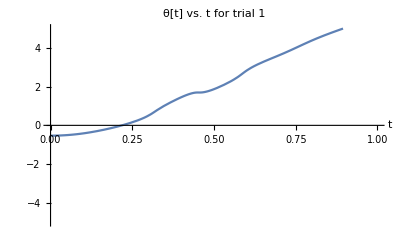

NDSolve::ndsz: At t == 2.49994, step size is effectively zero; singularity or stiff system suspected.

tfexp = 0.36856

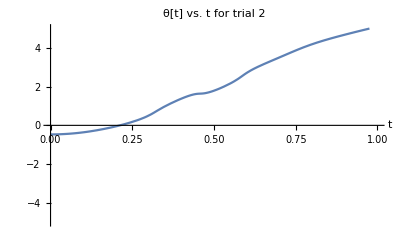

tfexp = 0.400705

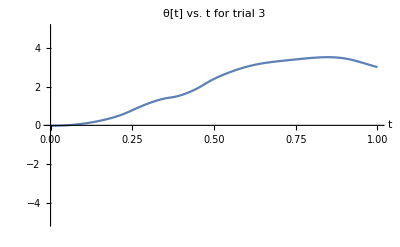

NDSolve::ndsz: At t == 2.50482, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

tfexp = 0.520894

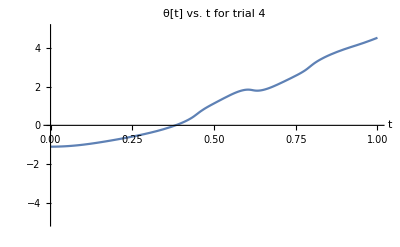

```mathematica
(* We need to invert θ[t] near tfexp so that we can determine δtfexp. So, we first find the region on which θ[t] is 1-1 in all simulations, so that we may invert θ[t]. *)
tfexpList={}; (* We'll use this later. Don't worry about it for now. *)
For[i=1,i≤4,i+=1,
{
outputs=simulateTrebuchet[α,expParams[[i]],0];
tfexp=outputs[[6]];
θ=outputs[[1]];
tfexpList=Append[tfexpList,tfexp];
Print["tfexp = ", tfexp];
Print[Plot[θ[t],{t,0,1},PlotRange->{-5,5},PlotLabel->StringForm["θ[t] vs. t for trial ``", i],AxesLabel->Automatic]];
}];
```

```mathematica
(* We see that θ[t] is 1-1 on the domain [0, .6] for each simulation, and that tfexp is contained within this domain for each simulation. Now we find θ^-1[θ] on the domain [0, .6]. *)
```

NDSolve::ndsz: At t == 2.06133, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-2.20066} lies outside the range of data in the interpolating function. Extrapolation will be used.

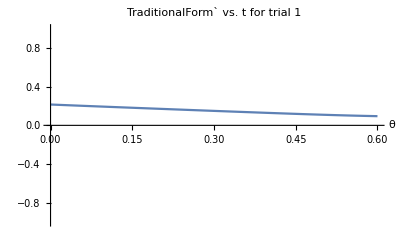

NDSolve::ndsz: At t == 2.49994, step size is effectively zero; singularity or stiff system suspected.

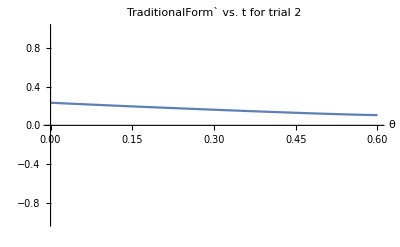

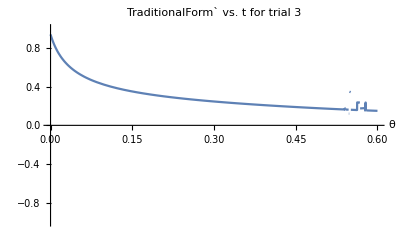

NDSolve::ndsz: At t == 2.50482, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

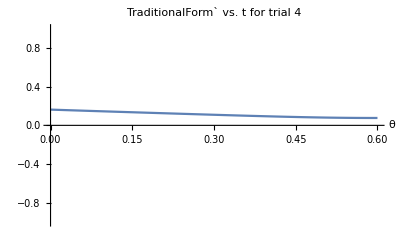

```mathematica
For[i=1,i≤4,i+=1,
{
θ=simulateTrebuchet[α,expParams[[i]],0][[1]];
θinv=InverseFunction[θ];
Print[Plot[Abs[θinv'[θ]],{θ,0,.6},PlotRange->{-1,1},PlotLabel->StringForm["TraditionalForm` vs. t for trial ``",i],AxesLabel->Automatic]];(* Invert θ on the domain [0, .5] and plot its derivative. *)
}];
```

We see that in all cases, |(∂θ^-1(θ))/(∂θ)| is bounded above by 1. Therefore, using that ∂θfexp=.002 rad (experimentally determined), we have ∂tfexp=|(∂θ^-1(θ))/(∂θ)|∂θfexp≤1*(.002)=.002.
Therefore ∂vmf=|(∂vmf)/(∂t)|∂tfexp≤ .002|(∂vmf)/(∂t)|.
Our last task is to find |(∂vmf)/(∂t)| at each value of tfexp (we stored tfexp in the list tfexpList for this purpose), and pick the maximum value as an upper bound.

```mathematica
(* For each simulation, plot |(∂vmf)/(∂t)| and print the values of this function at the various tfexp's. *)
```

NDSolve::ndsz: At t == 2.06133, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-2.20066} lies outside the range of data in the interpolating function. Extrapolation will be used.

TraditionalForm`|_(t = tfexp coorresp to trial RowBox[{) vs. t for trial 3.81683

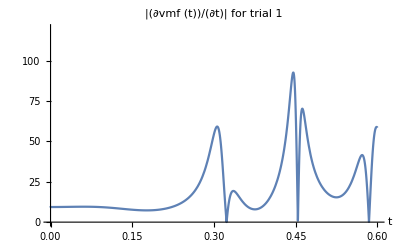

NDSolve::ndsz: At t == 2.49994, step size is effectively zero; singularity or stiff system suspected.

TraditionalForm`|_(t = tfexp coorresp to trial RowBox[{) vs. t for trial 3.69691

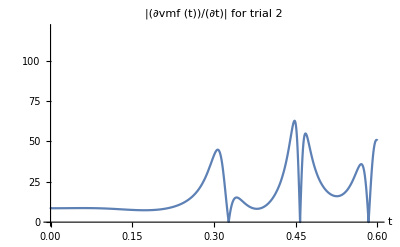

TraditionalForm`|_(t = tfexp coorresp to trial RowBox[{) vs. t for trial 2.92654

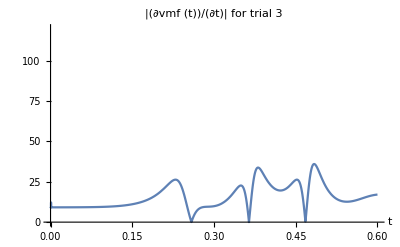

NDSolve::ndsz: At t == 2.50482, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

TraditionalForm`|_(t = tfexp coorresp to trial RowBox[{) vs. t for trial 3.58293

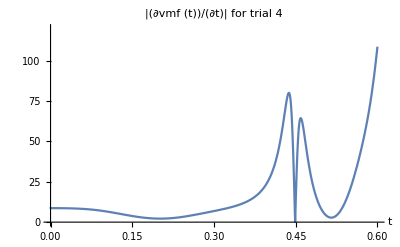

TraditionalForm`|_(t = tfexp\ coorresp\ to\ trial\ 1) vs. t for trial 3.81683

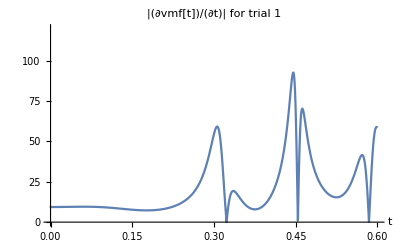

NDSolve::ndsz: At t == 2.49994, step size is effectively zero; singularity or stiff system suspected.

TraditionalForm`|_(t = tfexp coorresp to trial RowBox[{) vs. t for trial 3.69691

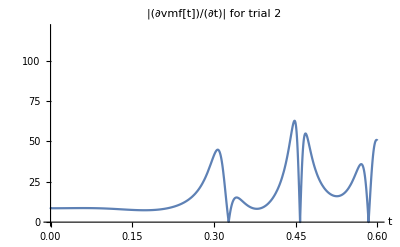

TraditionalForm`|_(t = tfexp coorresp to trial RowBox[{) vs. t for trial 2.92654

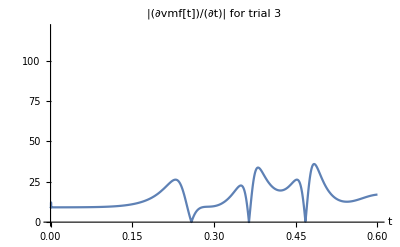

NDSolve::ndsz: At t == 2.50482, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

TraditionalForm`|_(t = tfexp coorresp to trial RowBox[{) vs. t for trial 3.58293

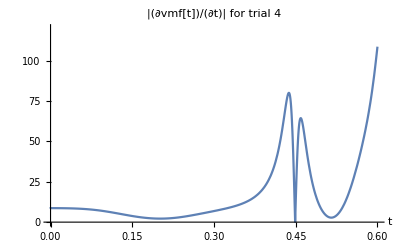

```mathematica
For[i=1,i≤4,i+=1,
{
vmffn=simulateTrebuchet[α,expParams[[i]],0][[5]]; (* This time, we have extracted the 5th ouput, vmf[t]. *)
tfexp=tfexpList[[i]];
Print[StringForm["TraditionalForm`|_(t = tfexp coorresp to trial ``) vs. t for trial ",i], vmffn[tfexp]];
Print[Plot[Abs[vmffn'[t]],{t,0,.6},PlotRange->{0,120},PlotLabel->StringForm["|(∂vmf (t))/(∂t)| for trial ``", i],AxesLabel->Automatic]]; (* Invert θ on the domain [0, .5] and plot its derivative. Again, we plot on [0, .6] because the release time tfexp is in the range [0, .6]. *)
}];
```

While these plots look kind of crazy, we see that|(∂vmf(t))/(∂t)| is at most 3.6 m/s at the experimentally determined release times for each simulation.
Therefore,  ∂vmf=|(∂vmf)/(∂t)|∂tfexp≤ .002|(∂vmf)/(∂t)|≤ .002 * 3.6  m/s= .0072 m/s.